# Inlämningsuppgift 1

Dana Ghafour, TIDAB, danagf@ug.kth.se
Sophie Malmberg, TIDAB, sophiema@ug.kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

```mathematica
Följande polynomekvation ska lösas genom att hitta lösningarna:
```

```mathematica
2 x^4-(74 x^3)/3+(253 x^2)/6+(111 x)/2-105=0
```

Sedan ska en graf plottas för polynomet och nollställen ska markeras med röda punkter.

### Resultat

#### Lösning

Lösningarna för ekvationen kan fås genom att skriva:

```mathematica
x/.Solve[2 x^4-(74 x^3)/3+(253 x^2)/6+(111 x)/2-105==0]
```

{-3/2,3/2,7/3,10}

Lösningen till funktionen är x=-3/2∨x=3/2∨x=7/3∨x=10.
Sen kan man testa om polynomekvationen blir lika med noll för dessa x - värden genom att skriva:

```mathematica
2 x^4-74 x^3/3+253 x^2/6+111 x/2-105==0/.{{x->-3/2}, {x->3/2}, {x->7/3}, {x->10}}
```

{True,True,True,True}

## Graf

Funktionen har nollställen markerat på x-axeln med röda punkter enligt nedanstående graf:

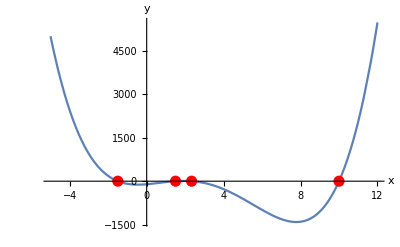

```mathematica
Plot[2x^4-74x^3/3+253x^2/6+111x/2-105,{x,-5,12},AxesLabel->{"x","y"},Epilog->({Red,PointSize[0.02],Point[{x1,0}], Point[{x2,0}],Point[{x3,0}],Point[{x4,0}]}/.
AssociationThread[{x1,x2,x3,x4},
SolveValues[2x^4-74x^3/3+253x^2/6+111x/2-105==0,x]])]
```

Grafen till funktionen f(x)=2 x^4-(74 x^3)/3+(253 x^2)/6+(111 x)/2-105.

## Kod

```mathematica
x/.Solve[2 x^4-(74 x^3)/3+(253 x^2)/6+(111 x)/2-105==0]
2 x^4-74 x^3/3+253 x^2/6+111 x/2-105==0/.{{x->-3/2}, {x->3/2}, {x->7/3}, {x->10}}
Plot[2x^4-74x^3/3+253x^2/6+111x/2-105,{x,-5,12},AxesLabel->{"x","y"},Epilog->({Red,PointSize[0.02],Point[{x1,0}], Point[{x2,0}],Point[{x3,0}],Point[{x4,0}]}/.
AssociationThread[{x1,x2,x3,x4},
SolveValues[2x^4-74x^3/3+253x^2/6+111x/2-105==0,x]])]
```

Uppgift 2: Binomisk ekvation

## Sammanfattning

### Uppgift

Lösningen ska hittas till ekvationen z^5 = -3+3I och sedan grafiskt visa att lösningarna ligger på en cirkel i det komplexa talplanet.

### Resultat

#### Lösning

```mathematica
Z=N[SolveValues[z^5==-3+3ⅈ,z, Complexes]]
```

{1.18962+0.606141 ⅈ,-0.208862+1.3187 ⅈ,0.944088-0.944088 ⅈ,-1.3187+0.208862 ⅈ,-0.606141-1.18962 ⅈ}

## Graf

Lokaliserar lösningen till ekvationen z^5 = -3 + 3i på grafen.

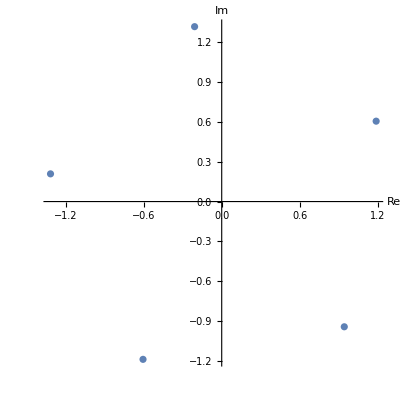

```mathematica
ComplexListPlot[Z=SolveValues[z^5==-3+3ⅈ,z, Complexes],AxesLabel->{"Re", "Im"}]
```

Visar grafiskt att lösningarna ligger på en cirkel i det komplexa talplanet.

{(-3+3 ⅈ)^(1/5),(-3+3 ⅈ)^(1/5) (-1)^(2/5),-(-3+3 ⅈ)^(1/5) (-1)^(3/5),(-3+3 ⅈ)^(1/5) (-1)^(4/5),-(-3)^(1/5) (-1+ⅈ)^(1/5)}

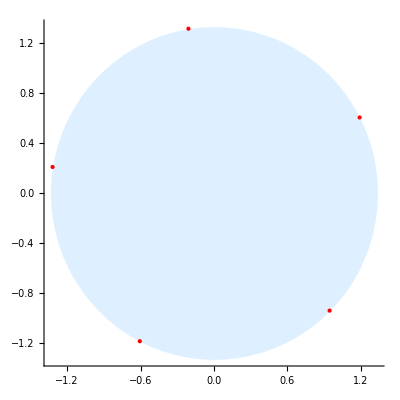

```mathematica
Lös=SolveValues[z^5==-3+3*I, z]
f1=ComplexListPlot[Lös,PlotStyle->{Red,PointSize[Large]}]; 
f2 = Graphics[{LightBlue, Disk[{0,0}, Abs[Lös[[1]]]]}, Axes->True];
Show[f2,f1, PlotRange->Automatic]
```

## Kod

```mathematica
ComplexListPlot[Z=SolveValues[z^5==-3+3ⅈ,z, Complexes],AxesLabel->{"Re", "Im"}]
Lös=SolveValues[z^5==-3+3*I, z]
f1=ComplexListPlot[Lös]; 
f2 = Graphics[{LightBlue, Disk[{0,0}, Abs[Lös[[1]]]]}, Axes->True];
Show[f2,f1, PlotRange->Automatic]
```

Uppgift 3 - Olikheter

## Sammanfattning

### Uppgift

Målet är att lösa uppgifterna 21, 22, 25 och 26 i kapitel 3 i kurslitteraturen Matematisk kommunikation, argumentation och skapande . Uppgifterna består av olikheter som löses med hjälp av Mathematica - funktionen Reduce som resulterar i ett exakt värde eller intervall där olikheten är sann . Graferna skapas sedan med hjälp av funktionen Plot .

### Lösning

#### 21.a

Olikhet: (x-2)/(x^2+1)≥0, x∈ℝ 
Svar: x ≥ 2

```mathematica
Reduce[(x-2)/((x^2)+1)>=0,{x} ]
```

x≥2

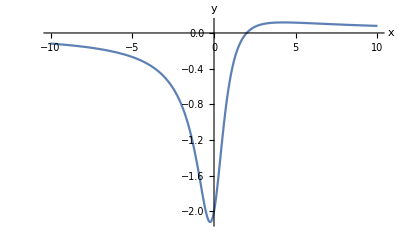

```mathematica
Plot[(x-2)/((x^2)+1), {x,-10,10},AxesLabel->{"x","y"}]
```

Grafen till funktionen f(x)=(x-2)/(x^2+1)

#### 21. b

Olikhet: 2/(3 x-1)≤1, x∈ℝ
Svar: x<1/3||x≥1

```mathematica
Reduce[2/(3x-1) <= 1, {x}]
```

x<1/3||x≥1

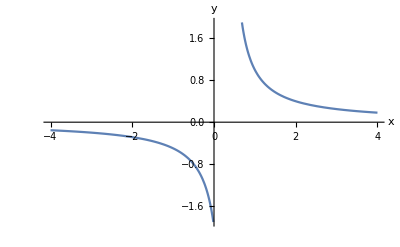

```mathematica
Plot[(2/(3x-1)), {x,-4,4},AxesLabel->{"x","y"}]
```

Grafen till funktionen f(x)=2/(3 x-1)

#### 21. c

Olikhet: 4/(x^2+4)≥1/2, x∈ℝ 
Svar: -2≤ x ≤2

```mathematica
Reduce[4/(x^2+4)>=1/2, {x}]
```

-2≤x≤2

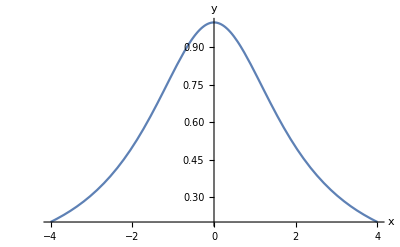

```mathematica
Plot[4/(x^2+4), {x,-4,4},AxesLabel->{"x","y"}]
```

Grafen till funktionen  f(x)=4/(x^2+4)

#### 21.d

Olikhet: (x-2)/(x^2-1)≥0, x∈ℝ 
Svar: -1< x <1 || x≥2

```mathematica
Reduce[(x-2)/(x^2-1)>=0, {x}]
```

-1<x<1||x≥2

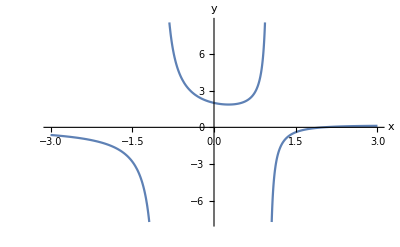

```mathematica
Plot[(x-2)/(x^2-1), {x,-3,3},AxesLabel->{"x","y"}]
```

Grafen till funktionen  f(x)=(x-2)/(x^2-1)

#### 21.e

Olikhet: (x-2)/(x-1)≥(2 x)/(x+1)+1, x∈ℝ 
Svar: -1< x <1

```mathematica
Reduce[((x-2)/(x-1))>=1+(2x/(x+1)), {x}]
```

```mathematica
-1<x<1
```

```mathematica
p1 = Plot[((x-2)/(x-1)), {x,-4,4},AxesLabel->{"x","y"}]
```

```mathematica
p2 = Plot[1+(2x/(x+1)), {x,-4,4},AxesLabel->{"x","y"}, PlotStyle->Red]
```

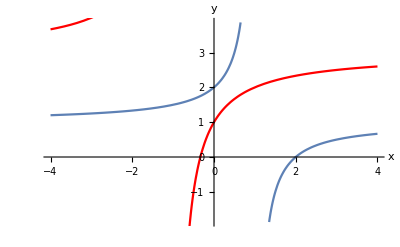

```mathematica
Show[p1,p2]
```

Grafen till funktionen f(x)=(x-2)/(x-1) (blå)  samt g(x)=(2 x)/(x+1)+1 (röd)

#### 22.a

Olikhet: √(x+1)≤-√(x+2), x∈ℝ
Svar: Det finns inget värde på x där olikheten är sann.

```mathematica
Reduce[Sqrt[x+1] <= -Sqrt[2+x], {x}]
```

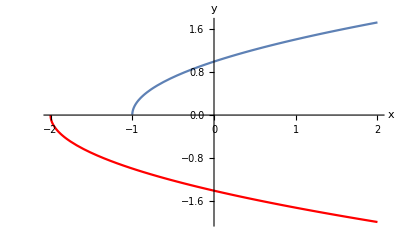

```mathematica
False
p1 = Plot[Sqrt[x+1], {x,-2,2},AxesLabel->{"x","y"}]
p2 = Plot[ -Sqrt[2+x], {x,-2,2},AxesLabel->{"x","y"}, PlotStyle->Red]
Show[p1,p2, PlotRange->Automatic]
```

Grafen till funktionen f(x)=√(x+1) (blå)  samt g(x)=-√(x+2) (röd)

#### 22.b

Olikhet: √(2 x-1)>-√(3-x),  x∈ℝ
Svar: 1/2≤x≤3

```mathematica
Reduce[Sqrt[2x-1]> -Sqrt[3-x],{x}]
```

1/2≤x≤3

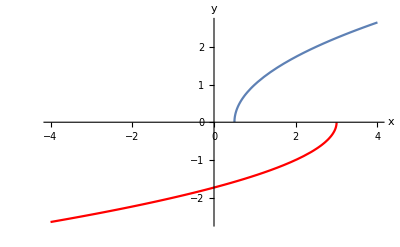

```mathematica
p1 = Plot[Sqrt[2x-1], {x,-4,4},AxesLabel->{"x","y"}]
p2 = Plot[-Sqrt[3-x], {x,-4,4},AxesLabel->{"x","y"}, PlotStyle->Red]
Show[p1,p2, PlotRange->Automatic]
```

Grafen till funktionen f(x)=√(2 x-1) (blå)  samt g(x)=-√(3-x) (röd)

#### 22.c

Olikhet: √(x^2-1)≥√(2 x^2-2 x,) x ∈ ℝ
Svar: x = 1

```mathematica
Reduce[Sqrt[x^2-1]>= Sqrt[2x^2-2x], {x}]
```

x==1

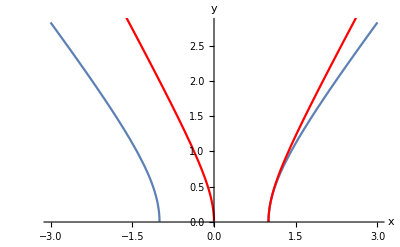

```mathematica
p1 = Plot[Sqrt[x^2-1], {x,-3,3},AxesLabel->{"x","y"}]
p2 = Plot[Sqrt[2x^2-2x], {x,-3,3},AxesLabel->{"x","y"}, PlotStyle->Red]
Show[p1,p2]
```

Grafen till funktionen f(x)=√(x^2-1) (blå)  samt g(x)=√(2 x^2-2 x) (röd)

#### 22.d

Olikhet: √x+2≥x, x∈ℝ
Svar: 0 ≤ x ≤ 4

```mathematica
Reduce[2+Sqrt[x]>= x, {x}]
```

0≤x≤4

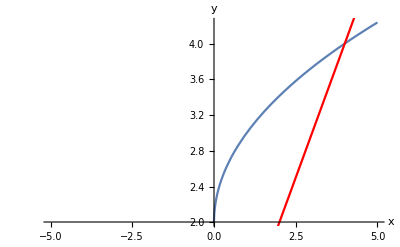

```mathematica
p1 = Plot[2+Sqrt[x], {x,-5,5},AxesLabel->{"x","y"}]
p2 = Plot[x, {x,-5,5},AxesLabel->{"x","y"}, PlotStyle->Red]
Show[p1,p2]
```

Grafen till funktionenf(x)=√x+2(blå) samtg(x)=x(röd)

#### 25

Olikhet: (x^2+1)^2-4 (x^2+1)≥5, x∈ℝ
Svar: x ≤ -2 || x ≥ 2

```mathematica
Reduce[(x^2+1)^2-4(x^2+1)>=5, {x}]
```

x≤-2||x≥2

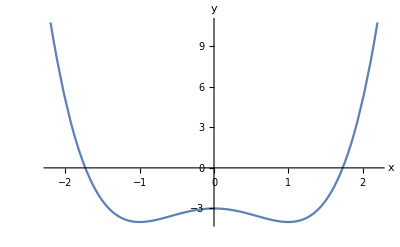

```mathematica
x≤-2||x≥2
Plot[(x^2+1)^2-4(x^2+1), {x,-2.2,2.2},AxesLabel->{"x","y"}]
```

Grafen till funktionenf(x)=(x^2+1)^2-4 (x^2+1)

#### 26.a

Olikhet: |x-2|+|x-1|==5, x∈ ℝ
Svar: Mathematicas funktion Reduce resulterar i både ett reellt intervall för x och ett imaginärt värde. Eftersom vi i detta fall endast är intresserade av reella värden är svaret x = -1 eller x = 4.

```mathematica
Reduce[Abs[x-1]+Abs[x-2]==5, {x}]
```

-1≤Re[x]≤4&&(Im[x]==-1/5 √(96+72 Re[x]-24 Re[x]^2)||Im[x]==1/5 √(96+72 Re[x]-24 Re[x]^2))

```mathematica
Reduce[Abs[x-1]+Abs[x-2]==5, {x},Reals]
```

x==-1||x==4

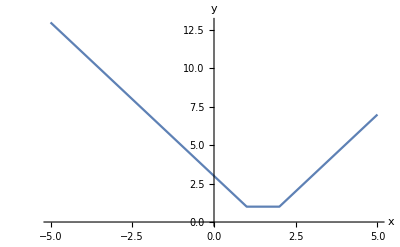

```mathematica
Plot[Abs[x-1]+Abs[x-2], {x,-5,5},AxesLabel->{"x","y"}]
```

Grafen till funktionenf(x)=|x-2|+|x-1|

#### 26.b

Olikhet: Abs[x^2-x-2]==2, x∈ℝ
Svar: Mathematicas funktion Reduce resulterar i både ett reellt intervall för x och ett imaginärt värde. Eftersom vi i detta fall endast är intresserade av reella värden är svaret x==0||x==1||x==1/2 (1-√17)||x==1/2 (1+√17)

```mathematica
Reduce[Abs[x^2-x-2]==2, {x}]
```

(1/2 (1-√17)≤Re[x]≤0&&(Im[x]==-√(1/2 (-5+2 Re[x]-2 Re[x]^2)+1/2 √(25-36 Re[x]+36 Re[x]^2))||Im[x]==√(1/2 (-5+2 Re[x]-2 Re[x]^2)+1/2 √(25-36 Re[x]+36 Re[x]^2))))||(1≤Re[x]≤1/2 (1+√17)&&(Im[x]==-√(1/2 (-5+2 Re[x]-2 Re[x]^2)+1/2 √(25-36 Re[x]+36 Re[x]^2))||Im[x]==√(1/2 (-5+2 Re[x]-2 Re[x]^2)+1/2 √(25-36 Re[x]+36 Re[x]^2))))

```mathematica
Reduce[Abs[x^2-x-2]==2, {x}, Reals]
```

x==0||x==1||x==1/2 (1-√17)||x==1/2 (1+√17)

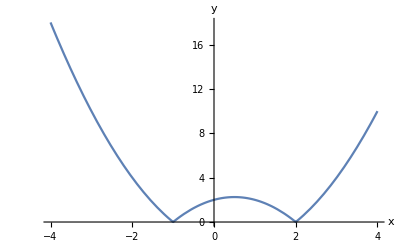

```mathematica
Plot[Abs[x^2-x-2], {x,-4,4},AxesLabel->{"x","y"}]
```

Grafen till funktionenf(x)=Abs[x^2-x-2]

Uppgift 4 - Arean av en cirkel och närmevärde till Pi

## Sammanfattning

### Uppgift

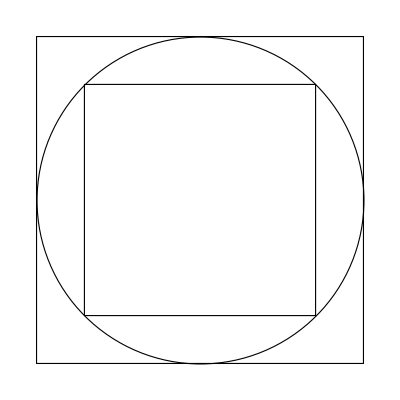
Målet med uppgiften är att approximera π genom att använda polygoner med fler än fyra sidor runt en cirkel och beräkna dess area. Sedan ska vi rita en graf för hur minimum och max-värdet för dessa areor konvergerar mot π areaenheter som en funktion av antalet polygoner.

-Graphics-

### Resultat

#### Matematisk modell

Vi utgår från en cirkel med radien r=1längdenhet och arean a=πr^2= π areaenheter.

Lösningen för uppgiften får vi först genom att räkna ut arean för polygonen innanför cirkeln. Varje sida av den n-sidiga polygonen går att dela upp i två rätvinkliga trianglar med en vinkel α_t=(π/n).  Hypotenusan av trianglarna är  i detta fall  lika med radien som är 1 längdenhet. Triangelns höjd är lika med sin (π/n) och dess bredd är  cos (π/n). Arean av en triangel blir då a_t=(cos (π/n)sin (π/n))/2. För att bestämma arean av en polygon med n antal sidor innanför cirkeln kan vi då använda följande formel, där n är antalet sidor på polygonen:

a_i=n sin(π/n)cos(π/n)

På samma sätt kan vi bestämma  arean av en polygon med n antal sidor utanför cirkeln genom att använda följande formel (som vi kom fram till med hjälp av kursens lärare Fadil Galjic):

a_u=n tan(π/n)

Vi ritar en graf som visar hur värdet på arean går mot π för båda polygonerna när antalet sidor ökar. Den röda punkterna representerar den yttre polygonen, och de blå punkterna representerar den inre polygonen. Det numeriska värdet för π (3.141592654) är markerat med en grön linje.
Om vi väljer n = 50000, där n är antalet sidor, blir arean av den inre polygonen 3.141592645 areaneheter. 
Den yttre polygonens area är när n = 50000 blir 3.141592658 areaenheter. Talet pi är lika med 3.141592654. Det syns att polygonernas areor överensstämmer med 7 decimaler när n = 50 000.
 
Svar: Det går att approximera ett närmevärde för π genom att använda arean av två polygoner runt en cirkel. När antalet sidor ökar konvergerar polygonernas area mot värdet på π.

## Graf

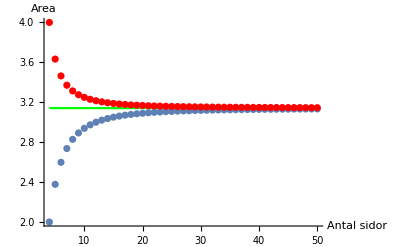

## Kod

```mathematica
areaInre[n_]:=n*Sin[Pi/n]*Cos[Pi/n]
```

```mathematica
areaYttre[n_]:= n*Tan[Pi/n]
```

```mathematica
N[areaInre[50000],10]
```

3.141592645

```mathematica
N[areaYttre[50000],10]
```

3.141592658

```mathematica
numPi = N[Pi,10]
```

3.141592654

```mathematica
numPi = N[Pi,10]
```

3.141592654

```mathematica
areaYttre[n_]:= n*Tan[Pi/n]
```

```mathematica
maxAntalSidor = 50;
```

```mathematica
pIn = Table[{x, areaInre[x]}, {x, 4, maxAntalSidor}]//N
```

```mathematica
pYt = Table[{x, areaYttre[x]}, {x, 4, maxAntalSidor}] //N
```

```mathematica
numPi = N[Pi,10]
```

```mathematica
linePi = Line[{numPi}]
```

Line[{3.141592654}]

```mathematica
plotIn = ListPlot[pIn,AxesLabel->{"Antal sidor","Area"}]
```

```mathematica
plotYt = ListPlot[pYt,AxesLabel->{"Antal sidor","Area"}, PlotStyle->Red]
```

```mathematica
plotPi = Plot[Pi, {n, 4, maxAntalSidor}, PlotStyle->Green]
```

```mathematica
Show[plotIn,plotYt, plotPi, PlotRange->Automatic]
```